# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Gegenbauer Scattering

```mathematica
pGegenbauer[u_,g_,a_]:=((1 + g^2-2 g u)^(-(a+1)))/((((1-g)^(-2 a)-(1+g)^(-2 a)) π)/(a g))
```

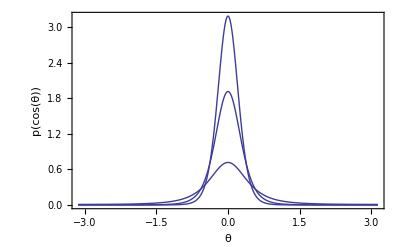

```mathematica
Show[
Plot[pGegenbauer[Cos[t],0.5,1],{t,-Pi,Pi},PlotRange->All],
Plot[pGegenbauer[Cos[t],0.5,3],{t,-Pi,Pi},PlotRange->All],
Plot[pGegenbauer[Cos[t],0.5,5],{t,-Pi,Pi},PlotRange->All],

Frame->True,
FrameLabel->{{p[Cos[θ]],},{θ,"Gegenbauer Scattering, G = 0.5, a = 1, 3, 5"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pGegenbauer[u,g,a],{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pGegenbauer[u,g,a],{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

((1+g)^(2 a) (1-2 a g+g^2)-(1-g)^(2 a) (1+2 a g+g^2))/(2 (-1+a) g ((1-g)^(2 a)-(1+g)^(2 a)))

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1) pGegenbauer[u,g,a]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

1

```mathematica
FullSimplify[Integrate[2Pi(2k+1) pGegenbauer[u,g,a]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->-1≤g≤1&&a>0]]
```

-(7 (24 a^2 g^2 (1+g^2) ((1-g)^(2 a)-(1+g)^(2 a))+3 (5+3 g^2+3 g^4+5 g^6) ((1-g)^(2 a)-(1+g)^(2 a))+8 a^3 g^3 ((1-g)^(2 a)+(1+g)^(2 a))+2 a g (15+14 g^2+15 g^4) ((1-g)^(2 a)+(1+g)^(2 a))))/(8 (-3+a) (-2+a) (-1+a) g^3 ((1-g)^(2 a)-(1+g)^(2 a)))

### sampling

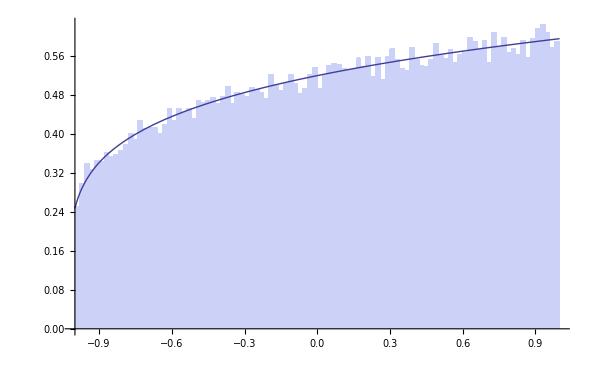

```mathematica
g=-0.8;
a=-1.2;
Show[Histogram[Map[(1+g^2-(# (1-g)^(-2 a)-(-1+#) (1+g)^(-2 a))^(-1/a))/(2 g)&,Table[RandomReal[],{i,1,100000}]],100,"PDF"],
Plot[2 Pi pGegenbauer[u,g,a],{u,-1,1},PlotRange->All]

]
Clear[g,a];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pGegenbauer[(1+g^2-(# (1-g)^(-2 a)-(-1+#) (1+g)^(-2 a))^(-1/a))/(2 g)&[ξ],g,a],Assumptions->a>0&&-1<g<1&&0<ξ<1]
```

(a g ((-(1+g)^(-2 a) (-1+ξ)+(1-g)^(-2 a) ξ)^(-1/a))^(-1-a))/(((1-g)^(-2 a)-(1+g)^(-2 a)) π)